```mathematica
ClearAll["Global`*"]

SetOptions[Plot,
PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick},{Cyan,Thick},{Purple,Thick}},
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->300];
SetOptions[ListPlot,
PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick},{Cyan,Thick},{Purple,Thick}},
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->300];
```

## DG Setup Data / Functions

#### Quadrature Data

```mathematica
GaussTrianglePts[4]={{0.44594849091597,0.44594849091597},{0.44594849091597,0.10810301816807},{0.10810301816807,0.44594849091597},{0.09157621350977,0.09157621350977},{0.09157621350977,0.81684757298046},{0.81684757298046,0.09157621350977}};
GaussTriangleWts[4]={0.22338158967801,0.22338158967801,0.22338158967801,0.10995174365532,0.10995174365532,0.10995174365532};

GaussBoundaryPts[2]={{0.21132486540518708},{0.7886751345948129}};
GaussBoundaryWts[2]={0.5,0.5};

GaussBoundaryPts[3]={{0.1127016653792583},{0.5},{0.8872983346207417}};
GaussBoundaryWts[3]={0.2777777777777778,0.4444444444444444,0.2777777777777778};

GaussBoundaryPts[4]={{0.0694318442029},{0.330009478},{0.669990521792428},{0.93056815579702628}};
GaussBoundaryWts[4]={0.1739274225687,0.326072577431273,0.32607257743127,0.173927422568726};
```

```mathematica
(*
int[{ξ1_,ξ2_}]=(a0+a1 ξ1+a2 ξ2+b1 ξ1^2+b2 ξ2^2+b3 ξ1 ξ2)(a0+a1 ξ1+a2 ξ2+b1 ξ1^2+b2 ξ2^2+b3 ξ1 ξ2);
Chop[Expand[
1/2 GaussTriangleWts[4].Map[int,GaussTrianglePts[4]]-Integrate[Integrate[int[{ξ1,ξ2}],{ξ1,0,1-ξ2}],{ξ2,0,1}]]]

int[{ξ1_}]=(a0+a1 ξ1+b1 ξ1^2)(a0+a1 ξ1+b1 ξ1^2);
Chop[Expand[
GaussBoundaryWts[3].Map[int,GaussBoundaryPts[3]]-Integrate[int[{ξ1}],{ξ1,0,1}]]]

int[{ξ1_}]=(a0+a1 ξ1+b1 ξ1^2)(a0+a1 ξ1+b1 ξ1^2);
Chop[Expand[
GaussBoundaryWts[2].Map[int,GaussBoundaryPts[2]]-Integrate[int[{ξ1}],{ξ1,0,1}]]]
*)
```

#### One Dimension, Vectorial Function

```mathematica
NN[1,{ξ1_}]=1;
NN[2,{ξ1_}]=ξ1;
NN[3,{ξ1_}]=ξ1^2;
NN[4,{ξ1_}]=ξ1^3-ξ1;
```

```mathematica
xVert[kk_]:=xa+(kk-1)dx;
ElemOfx[x_]:=Floor[(x-xa)/dx]+1;

Clear[pts,F1,F2,F2inv,F1inv,ξ,ξ1,ξ2]

F2[{ξ1_},nElem_]:=Block[{pts},
pts={{xa+(nElem-1)dx},{xa+nElem dx}};

pts⟦1⟧+ξ1(pts⟦2⟧-pts⟦1⟧)
];
F2inv[{x1_},nElem_]:=Block[{x0,dx1,dx2,det,pts},
pts={{xa+(nElem-1)dx},{xa+nElem dx}};

{(x1-pts⟦1,1⟧)/(pts⟦2,1⟧-pts⟦1,1⟧)}
];
```

```mathematica
GetAVis[n_]:=Block[{VertexRange,EdgeRange,coef},
VertexRange=Range[2,nVerts];
EdgeRange=Range[1,nEdges];
AVis=CoefficientArrays[Join[
{∑_(kk=1)^n coef[kk,1]NN[kk,F2inv[{xVert[1]},1]]},
Table[
Mean[{∑_(kk=1)^n coef[kk,ii-1]NN[kk,F2inv[{xVert[ii]},ii-1]],∑_(kk=1)^n coef[kk,ii]NN[kk,F2inv[{xVert[ii]},ii]]}]
,{ii,2,nElems}],
{∑_(kk=1)^n coef[kk,nElems]NN[kk,F2inv[{xVert[nElems+1]},nElems]]}
],Flatten[Table[Table[coef[kk,nrElem],{kk,1,n}],{nrElem,1,nElems}]]]⟦2⟧;
positions=Table[{xVert[ii]},{ii,1,nElems+1}];
];
```

```mathematica
Clear[u]
uAnsatz[{x1_},nr_]:=Block[{pt=F2inv[{x1},nr]},
Table[∑_(kk=1)^nb u[kk,m,nr]NN[kk,pt],{m,1,meqn}]
];
vTest[{x1_},nr_]:=Block[{pt=F2inv[{x1},nr]},
Table[Table[NN[jj,pt],{jj,1,nb}],{m,1,meqn}]
]
```

```mathematica
MatrixAbs[mat_]:=Block[{vals, vecs},
{vals, vecs} = Eigensystem[mat];
Simplify[Transpose[vecs].DiagonalMatrix[Abs[vals]].Inverse[Transpose[vecs]]]
];
```

```mathematica
orderInf[err_,nst_]:=Log[err⟦nst,4⟧/err⟦nst+1,4⟧]/Log[err⟦nst,3⟧/err⟦nst+1,3⟧]
order2[err_,nst_]:=Log[err⟦nst,5⟧/err⟦nst+1,5⟧]/Log[err⟦nst,3⟧/err⟦nst+1,3⟧]
```

# Simple Test Cases

## One-Dimensional

```mathematica
nb=3;
```

```mathematica
xa=-1.0;
xe=1.0;
```

```mathematica
nElems=50;
dx=(xe-xa)/nElems;
```

### 1D radial-sym Moment System (B1)

```mathematica
meqn=6;

R0=0.5;
R1=2.0;
τ=10.0;
ζ=0.0 10^-5;
χ=1.0;
v0=1;

α=1;
ζ0=0;

Ax={{0,1,0,0,0,0},{1,0,0,α,0,0},{0,0,0,0,α,0},{0,2/3,0,0,0,0},{0,0,1/2,0,0,0},{0,-1/3,0,0,0,0}};
Ar={{0,1,1,0,0,0},{0,0,0,α,α,-α},{-1,0,0,0,2 α,-α},{0,-1/3,-1/3,0,0,0},{0,-1/2,-1/2,0,0,0},{0,2/3,2/3,0,0,0}};
P={{ζ0,0,0,0,0,0},{0,ζ,0,0,0,0},{0,0,ζ,0,0,0},{0,0,0,α,0,0},{0,0,0,0,α,0},{0,0,0,0,0,α}};
Axmod=MatrixAbs[Ax]

F[r_]={0,0,0,0,0,0};


ϵ=10^-5;
{BCrhs,BC}={{vnW,-vtW/1},{{ϵ,-1,0,ϵ,0,0},{0,0,1/1,0,-ϵ,0}}};
X0=Transpose[{UnitVector[meqn,2],UnitVector[meqn,3]}];

Clear[θX,srX];
{θX[r_],srX[r_]}={0.-19.826662821093926/r-9.328292729012855 r,9.328292729012853*^6-(1.9826662821093928*^7)/r^2-(4.171731723043135*^10 BesselI[1,0.000447213595499958 r])/r+(8866.75327130804 BesselK[1,0.000447213595499958 r])/r};

{θX[r_],srX[r_]}={-(19.826662207239204507/r)-9.3282915644140603674 r,5.0652042525453294599+0.23326947772326773473/r^2-0.23320728911035150918 r^2+1.9826662207239204507 Log[r/10]};
xa=R0;
xe=R1;
```

{{√(3/5),0,0,√(3/5),0,0},{0,√(5/3),0,0,0,0},{0,0,1/(√2),0,0,0},{2/(√15),0,0,2/(√15),0,0},{0,0,0,0,1/(√2),0},{-1/(√15),0,0,-1/(√15),0,0}}

```mathematica
Do[
Do[
time=AbsoluteTiming[

dx=(xe-xa)/nElems;

vars=Flatten[Table[Table[Table[u[kk,m,nrElem],{m,1,meqn}],{kk,1,nb}],{nrElem,1,nElems}]];
Do[GetVar[m]=CoefficientArrays[Flatten[Table[Table[u[kk,m,nrElem],{kk,1,nb}],{nrElem,1,nElems}]],vars]⟦2⟧,{m,1,meqn}];

eqns=Table[0,{nrElem,1,nElems}];
Do[
U[r_]=uAnsatz[{r},nrElem];
dxU[r_]=D[U[r],{r,1}];

integrand[{r_}]=(Ax.dxU[r]+1/r Ar.U[r]+1/τ P.U[r]-F[r])vTest[{r},nrElem];
eqns⟦nrElem⟧+=Chop[Expand[dx GaussBoundaryWts[4].Map[integrand,Thread[F2[GaussBoundaryPts[4],nrElem],List,1]]]];

Do[
nrVert=nrElem+(1+(-1)^ii)/2;
normal=(-1)^ii;

UN[r_]=uAnsatz[{r},nrElem+(-1)^ii];

Flux[r_]=(normal Ax. ((U[r]+UN[r])/2)+Axmod.((U[r]-UN[r])/2));

If[(nrVert==1),
UN[r_]=U[r]-DiagonalMatrix[{1,normal,1,1,normal,1}].X0.Inverse[BC.X0].(BC.U[r]+BCrhs/.{vnW->0,vtW->0});
Flux[r_]=normal Ax.UN[r];
];

If[(nrVert==nElems+1),
UN[r_]=U[r]-DiagonalMatrix[{1,normal,1,1,normal,1}].X0.Inverse[BC.X0].(BC.U[r]+BCrhs/.{vnW->v0,vtW->-v0});
Flux[r_]=normal Ax.UN[r];
];

Flux[r_]=(normal Ax. ((U[r]+UN[r])/2)+Axmod.((U[r]-UN[r])/2));

integrand[{r_}]=(Flux[r]-normal Ax.U[r])vTest[{r},nrElem];

eqns⟦nrElem⟧+=Chop[Expand[integrand[{xVert[nrVert]}]]];

,{ii,1,2}]
,{nrElem,1,nElems}]
]⟦1⟧;
Print[{nElems,time}];

{b,A}=CoefficientArrays[Flatten[eqns],vars];

xsol=LinearSolve[A,-b];


UDG[r_]:=uAnsatz[{r},ElemOfx[r]]/.Thread[vars->xsol];
pos2=Flatten[Table[Table[{(xVert[j]+k/(nb+1)(xVert[j+1]-xVert[j]))},{k,1,nb}],{j,1,nElems}],1];
error1=Abs[Map[Apply[θX,#]&,pos2]-Map[Apply[UDG[#]⟦1⟧&,#]&,pos2]];
error2=Abs[Map[Apply[srX,#]&,pos2]-Map[Apply[UDG[#]⟦2⟧&,#]&,pos2]];

e1[nb,nElems]={nb,nElems,dx,Max[error1],Norm[dx error1]};
e2[nb,nElems]={nb,nElems,dx,Max[error2],Norm[dx error2]};
,{nElems,{40}}],
{nb,{4}}]
```

{40,1.72173}

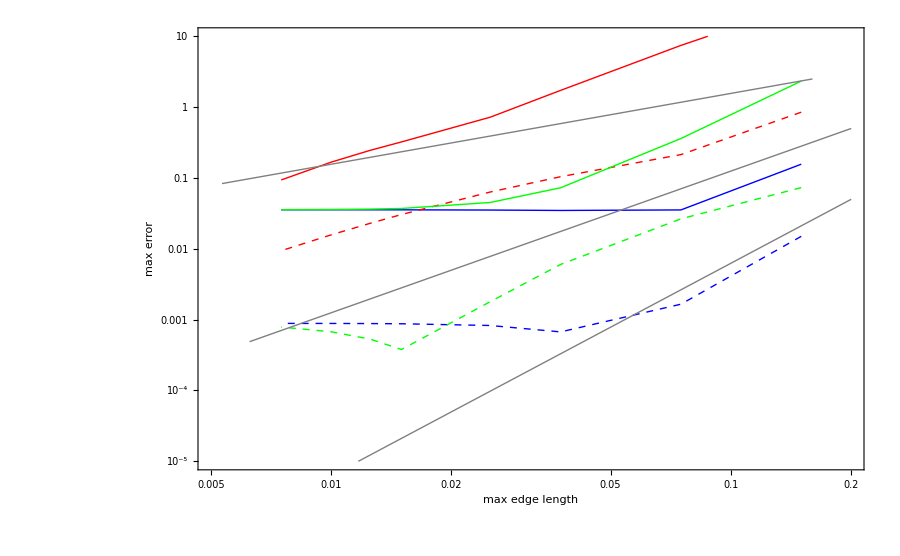

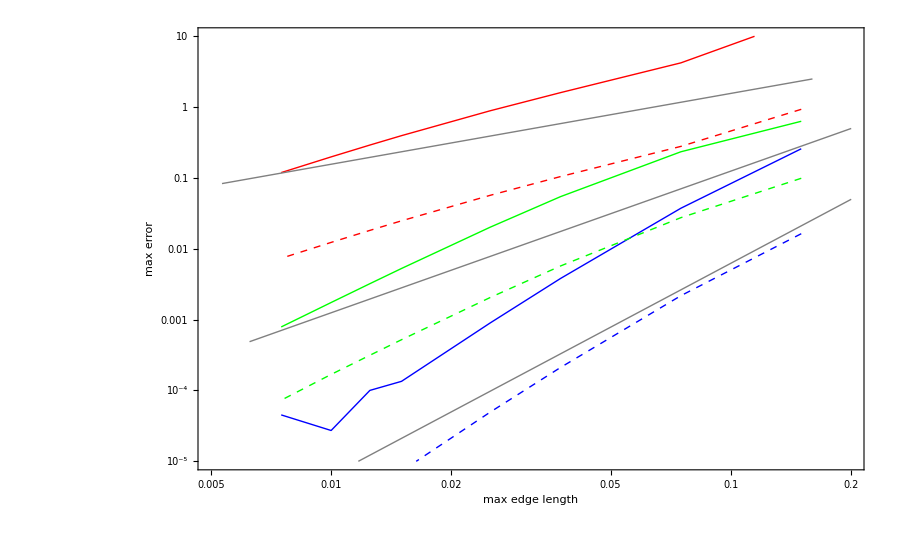

```mathematica
grids={10,20,40,60,100,120,150,200};
o1=2.5;
o2=0.5;
o3=0.05;

ListLogLogPlot[{Map[e1[4,#]⟦{3,4}⟧&,grids],Map[e2[4,#]⟦{3,4}⟧&,grids],Map[e1[2,#]⟦{3,4}⟧&,grids],Map[e2[2,#]⟦{3,4}⟧&,grids],Map[e1[3,#]⟦{3,4}⟧&,grids],Map[e2[3,#]⟦{3,4}⟧&,grids],{{0.16,o1},{0.16/30,o1/30}},{{0.2,o2},{0.2/32,o2/32^2}},{{0.2,o3},{0.2/32,o3/32^3}}},Joined->True,Frame->True,PlotStyle->{{Blue,Thick},{Blue,Thick,Dashed},{Red,Thick},{Red,Thick,Dashed},{Green,Thick},{Green,Thick,Dashed},{Gray,Thick},{Gray,Thick},{Gray,Thick}},PlotRange->{{0.005,0.2},{0.1 10^-4,10.0}},GridLines->Automatic,FrameLabel->{{"max error",""},{"max edge length","1D"}},BaseStyle->{Medium,FontFamily->"Helvetica"},ImageSize->900]
```

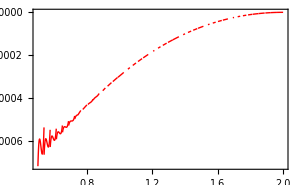

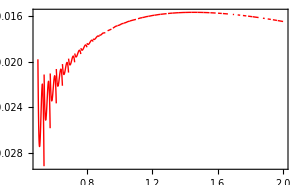

```mathematica
nb=4;
nElems=40;
Plot[{UDG[r]⟦2⟧-srX[r]},{r,R0,R1},PlotRange->All]
Plot[{UDG[r]⟦1⟧-θX[r]},{r,R0,R1},PlotRange->All]
```

```mathematica
θX=Interpolation[Table[{r,UDG[r]⟦1⟧},{r,R0,R1,0.001}],InterpolationOrder->1];
srX=Interpolation[Table[{r,UDG[r]⟦2⟧},{r,R0,R1,0.001}],InterpolationOrder->1];
```

```mathematica
θX=Interpolation[Table[{r,N[θX1[r],20]},{r,R0,R1,0.001}],InterpolationOrder->1];
srX=Interpolation[Table[{r,N[srX1[r],20]},{r,R0,R1,0.001}],InterpolationOrder->1];
```